```mathematica
SetSystemOptions["MKLThreads"->1];
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
```

### Get data on all the cases

```mathematica
SetSystemOptions["MKLThreads"->1];
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];

f[k_,n_]:=(k!)^k^(n-1)/k^n
fun[alpha_,n_]:=Module[{t,g,gp},t=Tuples[alpha,n];
g=Map[Function[x,{#,Take[Join[#,{x}],-n]}],alpha]&/@t;
gp=DirectedEdge@@@Join@@Map[StringJoin,g,{3}]]
seq[u_]:=Module[{tk},tk=u[[All,1]];
StringJoin@@{First@tk}~Join~(StringTake[#,-1]&/@Rest@tk)]
(*
grp=Graph[fun[{"0","1"},5]];
ham=FindHamiltonianCycle[grp,200];
dbseq=seq/@ham;
dbseq2=IntegerDigits/@ToExpression[dbseq];
dbseq5=dbseq2[[191;;200]];
dbseq5[[1]]//Length
*)
width=7;
dbseq5=Tuples[{0,1},width];
timesteps=2^width;

rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

releventCA={30,45,73,110,150,105,54,22,60,146,126,62,90,18,122,26,154,94,41,57,156,28,58,78,178,77,50,13,25,37,9,35,106,3,27,43,184,56,11,142,14,134,24,7,152,170,46,15,33,1,42,162,6,5,138,38,10,74,34,29,130,2,204,200,172,108,76,72,51,44,104,232,140,132,23,12,164,36,19,4,168,40,160,136,128,32,8,0};

rulecombinations=Tuples[releventCA,2];
```

```mathematica
Monitor[

OEEmini=
Flatten[
Table[Table[(*****environment setup*****)environmentrule=rulecombinations[[p,1]];
environment=CellularAutomaton[environmentrule,dbseq5[[a]],timesteps];(*ArrayPad[{1},(width-1)/2]*)partitions[i_]:=Tally[Partition[environment[[i]],3,1]];
numberofpartitions[i_]:=Length[Tally[Partition[environment[[i]],3,1]]];
f[x_]:=N[x/width,5];
thresholds[a_]:=MapAt[f,partitions[a],Flatten[Array[{#,2}&,{numberofpartitions[a],1}],1]];
(*****organism setup*****)rule=ruletable[[rulecombinations[[p,2]]+1]];
state=dbseq5[[a]];
initialstate=state;
g[x_]:=N[x/width,5];
(*****Run*****)smallsteps=Reap[Table[orgthresholds=MapAt[g,Tally[Partition[state,3,1]],Flatten[Array[{#,2}&,{Length[Tally[Partition[state,3,1]]],1}],1]];
fullcompare=Flatten[Select[Gather[Join[thresholds[j],orgthresholds]],Length[#]>1&]];
If[Length[fullcompare]>0,comparethetwo=Take[Flatten[Select[Gather[Join[thresholds[j],orgthresholds]],Length[#]>1&]],{4,-1,4}];
subrules2test=Flatten[Table[Position[subrules,fullcompare[[(1+8*(i-1));;((i-1)*8+3)]]],{i,1,Length[comparethetwo]/2}]];
subrulereplacements=If[Length[subrules2test]>0,Table[If[comparethetwo[[2*i-1]]≤comparethetwo[[2*i]],If[rule[[subrules2test[[i]],2]]==0,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]],If[rule[[subrules2test[[i]],2]]==1,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]]],{i,1,Length[subrules2test]}]];
newrule=ReplacePart[rule,Rule@@@Transpose[{subrules2test,subrulereplacements}]];
step=Nest[Partition[#,3,1,2]/.newrule&,state,1];
state=step;
rule=newrule;,step=Nest[Partition[#,3,1,2]/.rule&,state,1];
state=step;
rule=rule;];
Sow[step];
Sow[Position[ruletable,rule]-1],{j,1,timesteps}]];

(******Raw Data*******)CAorganism=Prepend[Take[Flatten[Last[smallsteps],1],{1,-1,2}],initialstate];
organismrules=Flatten[Take[Flatten[Last[smallsteps],1],{2,-1,2}]];

iniA=CAorganism[[1]];
iniB=ReplacePart[iniA,(width-1)/2->Abs[iniA[[(width-1)/2]]-1]];
Defects=ConstantArray[0,timesteps+1];
Defects[[1]]=Abs[iniA-iniB];
Do[ruleDef=IntegerDigits[organismrules[[b]],2,8];
rule=MapThread[#->#2&,{Tuples[{1,0},3],ruleDef}];
StateAN=Partition[Prepend[Append[iniA,Last[iniA]],First[iniA]],3,1]/.rule;
Defects[[b+1]]=Total[Abs[(Abs[Map[ConstantArray[#,3]&,Partition[Prepend[Append[iniA,Last[iniA]],First[iniA]],3,1]]-ConstantArray[{{1,0,0},{0,1,0},{0,0,1}},width]]/.rule)-StateAN]*Partition[Append[Prepend[Defects[[b]],First@Defects[[b]]],Last@Defects[[b]]],3,1],{2}];
iniA=StateAN;,{b,1,timesteps}];
lypdata=N@Log[Map[Total,Defects]]/Range[1,timesteps+1];


{dbseq5[[a]],rulecombinations[[p]],Last[lypdata],Length[Tally[CAorganism]],Length[Tally[organismrules]],Tally[organismrules]}

,{p,1,1000}],{a,1,Length[dbseq5]}],1];

,a]
```

```mathematica
Export["OEEminiall_1.out",OEEmini,"Table"]
```

OEEminiall_1.out

This outputs a table that shows {IC, Erule Orule, Lyp Value, #of states visited, #of rules visited, Tally rules {rule, #times visited} } for every possible integrated organism

%For rule loops, can we prove that there are alwasy closed rules? FOr OEE cases?
%What do these rule loops look like? Structure of OEE cases loops have self-sustaining loops, like autocatalytic sets
%Maybe do lyp analysis on rule loops

### Import the cases

```mathematica
in=Import["OEEminiall_1.out"];
in2=Import["OEEminiall_2.out"];
in3=Import["OEEminiall_3.out"];
in4=Import["OEEminiall_4.out"];
in5=Import["OEEminiall_5.out"];
in6=Import["OEEminiall_6.out"];
in7=Import["OEEminiall_7.out"];
in8=Import["OEEminiall_8.out"];
```

```mathematica
in[[1]]
```

{{0, 0, 0, 0, 0, 0, 0},{30, 30},-Infinity,2,2,{{31, 86}, {30, 42}}}

```mathematica
OEEmini1=
Table[

a=Flatten[
Table[
If[
StringQ[in[[j]][[i]]]==True,
If[in[[j]][[i]]=="-Infinity",
-∞,ToExpression[StringCases[in[[j]][[i]],
DigitCharacter..]]],
ToExpression[in[[j]][[i]]]
],
{i,1,Length[in[[j]]]}]
];
{a[[1;;7]],a[[8;;9]],a[[10;;12]],Partition[a[[13;;Length[a]]],2]}


,{j,1,Length[in]}];
```

```mathematica
OEEmini2=
Table[

a=Flatten[
Table[
If[
StringQ[in2[[j]][[i]]]==True,
If[in2[[j]][[i]]=="-Infinity",
-∞,ToExpression[StringCases[in2[[j]][[i]],
DigitCharacter..]]],
ToExpression[in2[[j]][[i]]]
],
{i,1,Length[in2[[j]]]}]
];
{a[[1;;7]],a[[8;;9]],a[[10;;12]],Partition[a[[13;;Length[a]]],2]}


,{j,1,Length[in2]}];
```

```mathematica
OEEmini3=
Table[

a=Flatten[
Table[
If[
StringQ[in3[[j]][[i]]]==True,
If[in3[[j]][[i]]=="-Infinity",
-∞,ToExpression[StringCases[in3[[j]][[i]],
DigitCharacter..]]],
ToExpression[in3[[j]][[i]]]
],
{i,1,Length[in3[[j]]]}]
];
{a[[1;;7]],a[[8;;9]],a[[10;;12]],Partition[a[[13;;Length[a]]],2]}


,{j,1,Length[in3]}];
```

```mathematica
OEEmini4=
Table[

a=Flatten[
Table[
If[
StringQ[in4[[j]][[i]]]==True,
If[in4[[j]][[i]]=="-Infinity",
-∞,ToExpression[StringCases[in4[[j]][[i]],
DigitCharacter..]]],
ToExpression[in4[[j]][[i]]]
],
{i,1,Length[in4[[j]]]}]
];
{a[[1;;7]],a[[8;;9]],a[[10;;12]],Partition[a[[13;;Length[a]]],2]}


,{j,1,Length[in4]}];
```

```mathematica
OEEmini5=
Table[

a=Flatten[
Table[
If[
StringQ[in5[[j]][[i]]]==True,
If[in5[[j]][[i]]=="-Infinity",
-∞,ToExpression[StringCases[in5[[j]][[i]],
DigitCharacter..]]],
ToExpression[in5[[j]][[i]]]
],
{i,1,Length[in5[[j]]]}]
];
{a[[1;;7]],a[[8;;9]],a[[10;;12]],Partition[a[[13;;Length[a]]],2]}


,{j,1,Length[in5]}];
```

```mathematica
OEEmini6=
Table[

a=Flatten[
Table[
If[
StringQ[in6[[j]][[i]]]==True,
If[in6[[j]][[i]]=="-Infinity",
-∞,ToExpression[StringCases[in6[[j]][[i]],
DigitCharacter..]]],
ToExpression[in6[[j]][[i]]]
],
{i,1,Length[in6[[j]]]}]
];
{a[[1;;7]],a[[8;;9]],a[[10;;12]],Partition[a[[13;;Length[a]]],2]}


,{j,1,Length[in6]}];
```

```mathematica
OEEmini7=
Table[

a=Flatten[
Table[
If[
StringQ[in7[[j]][[i]]]==True,
If[in7[[j]][[i]]=="-Infinity",
-∞,ToExpression[StringCases[in7[[j]][[i]],
DigitCharacter..]]],
ToExpression[in7[[j]][[i]]]
],
{i,1,Length[in7[[j]]]}]
];
{a[[1;;7]],a[[8;;9]],a[[10;;12]],Partition[a[[13;;Length[a]]],2]}


,{j,1,Length[in7]}];
```

```mathematica
OEEmini8=
Table[

a=Flatten[
Table[
If[
StringQ[in8[[j]][[i]]]==True,
If[in8[[j]][[i]]=="-Infinity",
-∞,ToExpression[StringCases[in8[[j]][[i]],
DigitCharacter..]]],
ToExpression[in8[[j]][[i]]]
],
{i,1,Length[in8[[j]]]}]
];
{a[[1;;7]],a[[8;;9]],a[[10;;12]],Partition[a[[13;;Length[a]]],2]}


,{j,1,Length[in8]}];
```

```mathematica
OEEminiall=Join[OEEmini1,OEEmini2,OEEmini3,OEEmini4,OEEmini5,OEEmini6,OEEmini7,OEEmini8];
Length[OEEminiall]
```

991232

### Make Lyp data for non-integrated organisms (ECAs)

991232

```mathematica
SetSystemOptions["MKLThreads"->1];
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];

width=7;
dbseq5=Tuples[{0,1},width];
timesteps=2^width;

rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

releventCA={30,45,73,110,150,105,54,22,60,146,126,62,90,18,122,26,154,94,41,57,156,28,58,78,178,77,50,13,25,37,9,35,106,3,27,43,184,56,11,142,14,134,24,7,152,170,46,15,33,1,42,162,6,5,138,38,10,74,34,29,130,2,204,200,172,108,76,72,51,44,104,232,140,132,23,12,164,36,19,4,168,40,160,136,128,32,8,0};

rulecombinations=Tuples[releventCA,2];
```

```mathematica
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];

width=7;
dbseq5=Tuples[{0,1},width];
timesteps=2^width;

rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

releventCA={30,45,73,110,150,105,54,22,60,146,126,62,90,18,122,26,154,94,41,57,156,28,58,78,178,77,50,13,25,37,9,35,106,3,27,43,184,56,11,142,14,134,24,7,152,170,46,15,33,1,42,162,6,5,138,38,10,74,34,29,130,2,204,200,172,108,76,72,51,44,104,232,140,132,23,12,164,36,19,4,168,40,160,136,128,32,8,0};

rulecombinations=Tuples[releventCA,2];

Monitor[
lypISO=Flatten[Table[
Table[
CAorganism=Prepend[CellularAutomaton[releventCA[[k]],dbseq5[[a]],timesteps],dbseq5[[a]]];
iniB=ReplacePart[dbseq5[[a]],(width-1)/2->Abs[dbseq5[[a]][[(width-1)/2]]-1]];
CAorganismiso=Prepend[CellularAutomaton[releventCA[[k]],iniB,timesteps],iniB];
Defects=Total/@Abs[CAorganismiso-CAorganism];
lypdata=Log[Defects]/Range[1,timesteps+2]//N;
Last[lypdata]

,{k,1,88}]
,{a,1,Length[dbseq5]}]];
,k]
```

```mathematica
lypISO//Tally
```

{{0.,2984},{0.0106638,808},{0.0149685,72},{0.0123803,308},{0.00845086,1392},{-∞,3302},{0.0053319,2282},{0.0137828,116}}

### Lyp Plot for Integrated vs. Isolated Organisms

{IC, Erule Orule, Lyp Value, #of states visited, #of rules visited, Tally rules {rule, #times visited} }

```mathematica
lypall1=Table[OEEminiall[[i]][[3]][[1]],{i,1,Length[OEEminiall]}];
```

```mathematica
lypall=lypall1/.-∞->-0.001/. 0.->0;
```

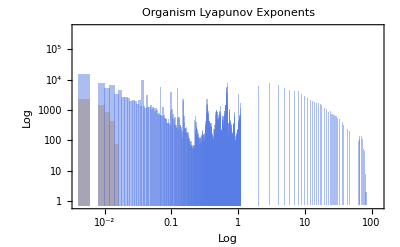

```mathematica
Histogram[{lypISO/.-∞->-0.001/. 0.->0,lypall},{0.002},PlotRange->All,ScalingFunctions->{"Log","Log"},PlotLabel->Style["Organism Lyapunov Exponents",FontSize->12],FrameLabel->{"Log","Log"},PlotTheme->"Business",ChartLegends->{Style["Integrated Organisms",FontSize->10],Style["OEE Integrated Organisms",FontSize->10],Style["Isolated Organisms",FontSize->10]}]
```

### Find OEE Cases 1

```mathematica
SetSystemOptions["MKLThreads"->1];
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

releventCA={30,45,73,110,150,105,54,22,60,146,126,62,90,18,122,26,154,94,41,57,156,28,58,78,178,77,50,13,25,37,9,35,106,3,27,43,184,56,11,142,14,134,24,7,152,170,46,15,33,1,42,162,6,5,138,38,10,74,34,29,130,2,204,200,172,108,76,72,51,44,104,232,140,132,23,12,164,36,19,4,168,40,160,136,128,32,8,0};

rulecombinations=Tuples[releventCA,2];

width=7;
dbseq5=Tuples[{0,1},width];
timesteps=(2^width);
```

```mathematica
OEEminipos=DeleteCases[Table[If[OEEminiall[[i]][[3]][[1]]>0,{OEEminiall[[i]][[1]],OEEminiall[[i]][[2]]}],{i,1,Length[OEEminiall]}],Null];
```

```mathematica
OEEminipos[[1]][[1]]
```

{0,0,0,0,0,0,0}

```mathematica
Monitor[
LYPINTOPOSS=DeleteCases[Table[

p=OEEminipos[[m]][[2]];
IC=OEEminipos[[m]][[1]];

(*****environment setup*****)environmentrule=p[[1]];
environment=CellularAutomaton[environmentrule,IC,timesteps];(*ArrayPad[{1},(width-1)/2]*)partitions[i_]:=Tally[Partition[environment[[i]],3,1]];
numberofpartitions[i_]:=Length[Tally[Partition[environment[[i]],3,1]]];
f[x_]:=N[x/width,5];
thresholds[a_]:=MapAt[f,partitions[a],Flatten[Array[{#,2}&,{numberofpartitions[a],1}],1]];
(*****organism setup*****)rule=ruletable[[p[[2]]+1]];
state=IC;
initialstate=state;
g[x_]:=N[x/width,5];

(*****Run*****)smallsteps=Reap[Table[orgthresholds=MapAt[g,Tally[Partition[state,3,1]],Flatten[Array[{#,2}&,{Length[Tally[Partition[state,3,1]]],1}],1]];
fullcompare=Flatten[Select[Gather[Join[thresholds[j],orgthresholds]],Length[#]>1&]];
If[Length[fullcompare]>0,comparethetwo=Take[Flatten[Select[Gather[Join[thresholds[j],orgthresholds]],Length[#]>1&]],{4,-1,4}];
subrules2test=Flatten[Table[Position[subrules,fullcompare[[(1+8*(i-1));;((i-1)*8+3)]]],{i,1,Length[comparethetwo]/2}]];
subrulereplacements=If[Length[subrules2test]>0,Table[If[comparethetwo[[2*i-1]]≤comparethetwo[[2*i]],If[rule[[subrules2test[[i]],2]]==0,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]],If[rule[[subrules2test[[i]],2]]==1,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]]],{i,1,Length[subrules2test]}]];
newrule=ReplacePart[rule,Rule@@@Transpose[{subrules2test,subrulereplacements}]];
step=Nest[Partition[#,3,1,2]/.newrule&,state,1];
state=step;
rule=newrule;,step=Nest[Partition[#,3,1,2]/.rule&,state,1];
state=step;
rule=rule;];
Sow[step];
Sow[Position[ruletable,rule]-1],{j,1,timesteps}]];

(******Raw Data*******)CAorganism=Prepend[Take[Flatten[Last[smallsteps],1],{1,-1,2}],initialstate];
organismrules=Flatten[Take[Flatten[Last[smallsteps],1],{2,-1,2}]];

If[Entropy[CAorganism]<4.816826532699039&&MemberQ[{{0,0,0,0,0,0,0},{1,1,1,1,1,1,1}},CAorganism[[-2]]]==False&&
(CAorganism[[-3]]===CAorganism[[-2]]===CAorganism[[-1]])==False,
m]

,{m,350001,415454}],Null]
,m]
```

{350001,350003,350004,350006,350007,350008,350009,350010,350011,350012,350013,350017,350018,350019,350020,350021,350022,350024,350025,350026,350028,350029,350030,42035,415047,415048,415049,415050,415051,415052,415053,415054,415056,415057,415059,415060,415061,415063,415064,415065,415066,415067,415069,415070,415071,415074,415076}
 |  |  |  |

```mathematica
Export["OEEcases8.out",LYPINTOPOSS,"Table"]
```

OEEcases8.out

Uses Entropy < 4.816826532699039, Ones that haven’t gone all black or white, and ones that don’t have the same last 3 repeating states

### Import OEE cases 1

```mathematica
oin=Import["OEEcases1.out","Table"]//Flatten;
```

```mathematica
oin2=Import["OEEcases2.out","Table"]//Flatten;
oin3=Import["OEEcases3.out","Table"]//Flatten;
oin4=Import["OEEcases4.out","Table"]//Flatten;
oin5=Import["OEEcases5.out","Table"]//Flatten;
oin6=Import["OEEcases6.out","Table"]//Flatten;
oin7=Import["OEEcases7.out","Table"]//Flatten;
oin8=Import["OEEcases8.out","Table"]//Flatten;
```

```mathematica
OEEcasesall=Join[oin,oin2,oin3,oin4,oin5,oin6,oin7,oin8];
Length[OEEminiall]
OEEcasesall//Length
```

991232

131181

### Verify OEE Cases 1 (make sure it captured the right thing)

```mathematica
OEEminipos=DeleteCases[Table[If[OEEminiall[[i]][[3]][[1]]>0,{OEEminiall[[i]][[1]],OEEminiall[[i]][[2]]}],{i,1,Length[OEEminiall]}],Null];
```

```mathematica
c=OEEminipos[[OEEcasesall[[6]]]];

OEEmini=
Flatten[
Table[(*****environment setup*****)environmentrule=c[[2]][[1]];
environment=CellularAutomaton[environmentrule,c[[1]],timesteps];(*ArrayPad[{1},(width-1)/2]*)partitions[i_]:=Tally[Partition[environment[[i]],3,1]];
numberofpartitions[i_]:=Length[Tally[Partition[environment[[i]],3,1]]];
f[x_]:=N[x/width,5];
thresholds[a_]:=MapAt[f,partitions[a],Flatten[Array[{#,2}&,{numberofpartitions[a],1}],1]];
(*****organism setup*****)rule=ruletable[[c[[2]][[2]]+1]];
state=c[[1]];
initialstate=state;
g[x_]:=N[x/width,5];
(*****Run*****)smallsteps=Reap[Table[orgthresholds=MapAt[g,Tally[Partition[state,3,1]],Flatten[Array[{#,2}&,{Length[Tally[Partition[state,3,1]]],1}],1]];
fullcompare=Flatten[Select[Gather[Join[thresholds[j],orgthresholds]],Length[#]>1&]];
If[Length[fullcompare]>0,comparethetwo=Take[Flatten[Select[Gather[Join[thresholds[j],orgthresholds]],Length[#]>1&]],{4,-1,4}];
subrules2test=Flatten[Table[Position[subrules,fullcompare[[(1+8*(i-1));;((i-1)*8+3)]]],{i,1,Length[comparethetwo]/2}]];
subrulereplacements=If[Length[subrules2test]>0,Table[If[comparethetwo[[2*i-1]]≤comparethetwo[[2*i]],If[rule[[subrules2test[[i]],2]]==0,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]],If[rule[[subrules2test[[i]],2]]==1,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]]],{i,1,Length[subrules2test]}]];
newrule=ReplacePart[rule,Rule@@@Transpose[{subrules2test,subrulereplacements}]];
step=Nest[Partition[#,3,1,2]/.newrule&,state,1];
state=step;
rule=newrule;,step=Nest[Partition[#,3,1,2]/.rule&,state,1];
state=step;
rule=rule;];
Sow[step];
Sow[Position[ruletable,rule]-1],{j,1,timesteps}]];

(******Raw Data*******)CAorganism=Prepend[Take[Flatten[Last[smallsteps],1],{1,-1,2}],initialstate];
organismrules=Flatten[Take[Flatten[Last[smallsteps],1],{2,-1,2}]];
ArrayPlot[CAorganism]
,{1}],1]
```

{-Graphics-}

### Longest trajecoties for ECA

```mathematica
IC=Tuples[{0,1},7];
AllECATraj=Table[Table[Length[Tally[CellularAutomaton[i,IC[[j]],2^7]]]
,{j,1,2^7}]
,{i,0,255}];
```

```mathematica
b=Position[AllECATraj//Flatten,AllECATraj//Flatten//Sort//Last]//Flatten;
```

```mathematica
AllECATraj//Flatten//Sort//Tally
```

{{1,1376},{2,4386},{3,4018},{4,2058},{5,1848},{6,1022},{7,3402},{8,4368},{9,1344},{10,308},{11,84},{12,56},{14,1946},{15,1372},{16,840},{17,448},{18,364},{19,280},{20,168},{21,224},{22,28},{23,28},{24,112},{25,84},{26,28},{27,56},{28,672},{29,224},{30,140},{31,140},{32,140},{49,196},{50,84},{51,28},{52,28},{53,28},{54,28},{63,252},{64,28},{65,28},{126,504}}

```mathematica
ECA7=Flatten[Table[Table[CellularAutomaton[i,IC[[j]],2^7]
,{j,1,2^7}]
,{i,0,255}],1];
```

```mathematica
Table[ECA7[[b[[i]]]]//ArrayPlot,{i,1,Length[b]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Compare trajectories and states, find out what longest trajectory is and how many states, use PRT thing

Longest trajectory is 126/128, but the patterns do not change, they only shift
Second longest is 65
Using 65 first, then distinguishing after

### Find OEE Cases 1I

```mathematica
SetSystemOptions["MKLThreads"->1];
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

releventCA={30,45,73,110,150,105,54,22,60,146,126,62,90,18,122,26,154,94,41,57,156,28,58,78,178,77,50,13,25,37,9,35,106,3,27,43,184,56,11,142,14,134,24,7,152,170,46,15,33,1,42,162,6,5,138,38,10,74,34,29,130,2,204,200,172,108,76,72,51,44,104,232,140,132,23,12,164,36,19,4,168,40,160,136,128,32,8,0};

rulecombinations=Tuples[releventCA,2];

width=7;
dbseq5=Tuples[{0,1},width];
timesteps=(2^width);
```

```mathematica
OEEminipos=DeleteCases[Table[If[OEEminiall[[i]][[3]][[1]]>0,{OEEminiall[[i]][[1]],OEEminiall[[i]][[2]]}],{i,1,Length[OEEminiall]}],Null];
```

```mathematica
Monitor[
LYPINTOPOSS=DeleteCases[Table[

p=OEEminipos[[OEEcasesall[[m]]]][[2]];
IC=OEEminipos[[OEEcasesall[[m]]]][[1]];

(*****environment setup*****)environmentrule=p[[1]];
environment=CellularAutomaton[environmentrule,IC,timesteps];(*ArrayPad[{1},(width-1)/2]*)partitions[i_]:=Tally[Partition[environment[[i]],3,1]];
numberofpartitions[i_]:=Length[Tally[Partition[environment[[i]],3,1]]];
f[x_]:=N[x/width,5];
thresholds[a_]:=MapAt[f,partitions[a],Flatten[Array[{#,2}&,{numberofpartitions[a],1}],1]];
(*****organism setup*****)rule=ruletable[[p[[2]]+1]];
state=IC;
initialstate=state;
g[x_]:=N[x/width,5];

(*****Run*****)smallsteps=Reap[Table[orgthresholds=MapAt[g,Tally[Partition[state,3,1]],Flatten[Array[{#,2}&,{Length[Tally[Partition[state,3,1]]],1}],1]];
fullcompare=Flatten[Select[Gather[Join[thresholds[j],orgthresholds]],Length[#]>1&]];
If[Length[fullcompare]>0,comparethetwo=Take[Flatten[Select[Gather[Join[thresholds[j],orgthresholds]],Length[#]>1&]],{4,-1,4}];
subrules2test=Flatten[Table[Position[subrules,fullcompare[[(1+8*(i-1));;((i-1)*8+3)]]],{i,1,Length[comparethetwo]/2}]];
subrulereplacements=If[Length[subrules2test]>0,Table[If[comparethetwo[[2*i-1]]≤comparethetwo[[2*i]],If[rule[[subrules2test[[i]],2]]==0,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]],If[rule[[subrules2test[[i]],2]]==1,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]]],{i,1,Length[subrules2test]}]];
newrule=ReplacePart[rule,Rule@@@Transpose[{subrules2test,subrulereplacements}]];
step=Nest[Partition[#,3,1,2]/.newrule&,state,1];
state=step;
rule=newrule;,step=Nest[Partition[#,3,1,2]/.rule&,state,1];
state=step;
rule=rule;];
Sow[step];
Sow[Position[ruletable,rule]-1],{j,1,timesteps}]];

(******Raw Data*******)CAorganism=Prepend[Take[Flatten[Last[smallsteps],1],{1,-1,2}],initialstate];
organismrules=Flatten[Take[Flatten[Last[smallsteps],1],{2,-1,2}]];

If[Length[Tally[CAorganism]]>65,{IC,p}]

,{m,1,2000}],Null]
,m]
```

```mathematica
Export["OEEcases2.out",LYPINTOPOSS,"Table"]
```

```mathematica
Length[OEEcasesall]
```

131181

### Prelim. examples

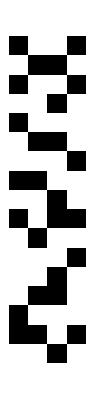
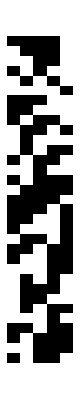
```mathematica
{41,33},-Graphics-,{13,5},-Graphics-,{42,184},-Graphics-,{42,154},-Graphics-,{11,32},-Graphics-
```

```mathematica
width=7;
dbseq5=Tuples[{0,1},width];
timesteps=(2^width);

p=Position[rulecombinations,{11,32}][[1]][[1]]
IC={0,1,1,1,1,1,0}

(*****environment setup*****)environmentrule=rulecombinations[[p,1]];
environment=CellularAutomaton[environmentrule,IC,timesteps];(*ArrayPad[{1},(width-1)/2]*)partitions[i_]:=Tally[Partition[environment[[i]],3,1]];
numberofpartitions[i_]:=Length[Tally[Partition[environment[[i]],3,1]]];
f[x_]:=N[x/width,5];
thresholds[a_]:=MapAt[f,partitions[a],Flatten[Array[{#,2}&,{numberofpartitions[a],1}],1]];
(*****organism setup*****)rule=ruletable[[rulecombinations[[p,2]]+1]];
state=IC;
initialstate=state;
g[x_]:=N[x/width,5];
(*****Run*****)smallsteps=Reap[Table[orgthresholds=MapAt[g,Tally[Partition[state,3,1]],Flatten[Array[{#,2}&,{Length[Tally[Partition[state,3,1]]],1}],1]];
fullcompare=Flatten[Select[Gather[Join[thresholds[j],orgthresholds]],Length[#]>1&]];
If[Length[fullcompare]>0,comparethetwo=Take[Flatten[Select[Gather[Join[thresholds[j],orgthresholds]],Length[#]>1&]],{4,-1,4}];
subrules2test=Flatten[Table[Position[subrules,fullcompare[[(1+8*(i-1));;((i-1)*8+3)]]],{i,1,Length[comparethetwo]/2}]];
subrulereplacements=If[Length[subrules2test]>0,Table[If[comparethetwo[[2*i-1]]≤comparethetwo[[2*i]],If[rule[[subrules2test[[i]],2]]==0,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]],If[rule[[subrules2test[[i]],2]]==1,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]]],{i,1,Length[subrules2test]}]];
newrule=ReplacePart[rule,Rule@@@Transpose[{subrules2test,subrulereplacements}]];
step=Nest[Partition[#,3,1,2]/.newrule&,state,1];
state=step;
rule=newrule;,step=Nest[Partition[#,3,1,2]/.rule&,state,1];
state=step;
rule=rule;];
Sow[step];
Sow[Position[ruletable,rule]-1],{j,1,timesteps}]];

(******Raw Data*******)CAorganism=Prepend[Take[Flatten[Last[smallsteps],1],{1,-1,2}],initialstate];
organismrules=Flatten[Take[Flatten[Last[smallsteps],1],{2,-1,2}]];

ArrayPlot[CAorganism]
f[x_]:=FromDigits[x,2]
(ByteCount[Compress[f/@CAorganism]]-ByteCount[Compress[ConstantArray[1,timesteps]]])/timesteps
```

3430

{0,1,1,1,1,1,0}

-Graphics-

37/16

```mathematica
ArrayPlot[CellularAutomaton[30,{0,0,1,1,1,0,1},2^7]]
```

-Graphics-

```mathematica
rulelabels=Table[IntegerDigits[i,2,8],{i,0,255}];
subrules=Reverse[Tuples[{0,1},3]];
ruletable=Table[Rule@@@Transpose[{subrules,rulelabels[[i]]}],{i,1,256}];

releventCA={30,45,73,110,150,105,54,22,60,146,126,62,90,18,122,26,154,94,41,57,156,28,58,78,178,77,50,13,25,37,9,35,106,3,27,43,184,56,11,142,14,134,24,7,152,170,46,15,33,1,42,162,6,5,138,38,10,74,34,29,130,2,204,200,172,108,76,72,51,44,104,232,140,132,23,12,164,36,19,4,168,40,160,136,128,32,8,0};

rulecombinations=Tuples[releventCA,2];

width=7;
dbseq5=Tuples[{0,1},width];
timesteps=(2^width)*88;
```

```mathematica
Monitor[
DeleteCases[Table[

p=OEEminiall[[m]][[1]];
IC=OEEminiall[[m]][[2]];

(*****environment setup*****)environmentrule=p[[1]];
environment=CellularAutomaton[environmentrule,IC,timesteps];(*ArrayPad[{1},(width-1)/2]*)partitions[i_]:=Tally[Partition[environment[[i]],3,1]];
numberofpartitions[i_]:=Length[Tally[Partition[environment[[i]],3,1]]];
f[x_]:=N[x/width,5];
thresholds[a_]:=MapAt[f,partitions[a],Flatten[Array[{#,2}&,{numberofpartitions[a],1}],1]];
(*****organism setup*****)rule=ruletable[[p[[2]]+1]];
state=IC;
initialstate=state;
g[x_]:=N[x/width,5];
(*****Run*****)smallsteps=Reap[Table[orgthresholds=MapAt[g,Tally[Partition[state,3,1]],Flatten[Array[{#,2}&,{Length[Tally[Partition[state,3,1]]],1}],1]];
fullcompare=Flatten[Select[Gather[Join[thresholds[j],orgthresholds]],Length[#]>1&]];
If[Length[fullcompare]>0,comparethetwo=Take[Flatten[Select[Gather[Join[thresholds[j],orgthresholds]],Length[#]>1&]],{4,-1,4}];
subrules2test=Flatten[Table[Position[subrules,fullcompare[[(1+8*(i-1));;((i-1)*8+3)]]],{i,1,Length[comparethetwo]/2}]];
subrulereplacements=If[Length[subrules2test]>0,Table[If[comparethetwo[[2*i-1]]≤comparethetwo[[2*i]],If[rule[[subrules2test[[i]],2]]==0,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]],If[rule[[subrules2test[[i]],2]]==1,ReplacePart[rule,{subrules2test[[i]],2}->1][[subrules2test[[i]]]],ReplacePart[rule,{subrules2test[[i]],2}->0][[subrules2test[[i]]]]]],{i,1,Length[subrules2test]}]];
newrule=ReplacePart[rule,Rule@@@Transpose[{subrules2test,subrulereplacements}]];
step=Nest[Partition[#,3,1,2]/.newrule&,state,1];
state=step;
rule=newrule;,step=Nest[Partition[#,3,1,2]/.rule&,state,1];
state=step;
rule=rule;];
Sow[step];
Sow[Position[ruletable,rule]-1],{j,1,timesteps}]];

(******Raw Data*******)CAorganism=Prepend[Take[Flatten[Last[smallsteps],1],{1,-1,2}],initialstate];
organismrules=Flatten[Take[Flatten[Last[smallsteps],1],{2,-1,2}]];

If[Entropy[CAorganism]<4.816826532699039&&MemberQ[{{0,0,0,0,0,0,0},{1,1,1,1,1,1,1}},CAorganism[[-2]]]==False,
{ArrayPlot[CAorganism],m}]

,{m,{195,196,243,505,646,647,915,918,935,951,966,1051,1052,1130,1133,1205,1206,1207,1208,1209,1239,1240,1241,1242,1249,1250,1267,1268,1294,1322,1324,1350,1351,1375,1397,1408,1412,1413,1450,1455,1456,1484,1486,1538,1553,1554,1555,1556,1571,1648,1649,1661,1674,1675,1677,1678,1752,1753,1783,1784,1811,1950,2005,2006,2008,2009,2039,2040,2041,2042,2043,2044,2045,2046,2047,2049,2061,2063,2091,2155,2156,2158,2159,2219,2221,2222,2254,2255,2256,2276,2279,2280,2282,2283,2380,2381,2382,2389,2406,2436,2437,2461,2462,2463,2466,2472,2561,2586,2656,2260,2726,2727,2728,2758,2800,2803,2804,2806,2847,2850,2851,2865,2888,2890,2892,2905,2921,2933,2940,2942,2944,1945,2947,2948,2954,2958,2966,2977,2978,2979,2980,2981,2982,2983,2984,2985,2986,2987,2988,2989,2990,2991,2992,2996,3000,3002,3003,3006,3007,3008,3012,3013,3019,3020}}],Null]
,m]
```

{{-Graphics-,243},{-Graphics-,505},{-Graphics-,935},{-Graphics-,951},{-Graphics-,966},{-Graphics-,1130},{-Graphics-,1133},{-Graphics-,1207},{-Graphics-,1208},{-Graphics-,1209},{-Graphics-,1241},{-Graphics-,1294},{-Graphics-,1375},{-Graphics-,1397},{-Graphics-,1412},{-Graphics-,1413},{-Graphics-,1455},{-Graphics-,1456},{-Graphics-,1553},{-Graphics-,1554},{-Graphics-,1555},{-Graphics-,1556},{-Graphics-,1571},{-Graphics-,1648},{-Graphics-,1649},{-Graphics-,1661},{-Graphics-,1675},{-Graphics-,1678},{-Graphics-,1752},{-Graphics-,1753},{-Graphics-,1783},{-Graphics-,1784},{-Graphics-,1950},{-Graphics-,2005},{-Graphics-,2006},{-Graphics-,2008},{-Graphics-,2009},{-Graphics-,2039},{-Graphics-,2040},{-Graphics-,2041},{-Graphics-,2049},{-Graphics-,2061},{-Graphics-,2063},{-Graphics-,2091},{-Graphics-,2156},{-Graphics-,2159},{-Graphics-,2219},{-Graphics-,2276},{-Graphics-,2380},{-Graphics-,2381},{-Graphics-,2382},{-Graphics-,2436},{-Graphics-,2437},{-Graphics-,2461},{-Graphics-,2462},{-Graphics-,2463},{-Graphics-,2466},{-Graphics-,2472},{-Graphics-,2561},{-Graphics-,2586},{-Graphics-,2656},{-Graphics-,2260},{-Graphics-,2800},{-Graphics-,2803},{-Graphics-,2806},{-Graphics-,2847},{-Graphics-,2850},{-Graphics-,2851},{-Graphics-,2865},{-Graphics-,2905},{-Graphics-,2921},{-Graphics-,2933},{-Graphics-,2942},{-Graphics-,2944},{-Graphics-,1945},{-Graphics-,2948},{-Graphics-,2954},{-Graphics-,2977},{-Graphics-,2978},{-Graphics-,2979},{-Graphics-,2980},{-Graphics-,2981},{-Graphics-,2982},{-Graphics-,2986},{-Graphics-,2987},{-Graphics-,2990},{-Graphics-,2991},{-Graphics-,3002},{-Graphics-,3003},{-Graphics-,3006},{-Graphics-,3007},{-Graphics-,3008},{-Graphics-,3012},{-Graphics-,3013},{-Graphics-,3019},{-Graphics-,3020}}